### Computational Teleology

```mathematica
Table[ArrayPlot[CellularAutomaton[{1340716537107,3},{Append[Table[1,n],2],0},200]],{n,30}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
all = ResourceData["Three-Color Cellular Automaton Rules that Double Their Input"];
```

```mathematica
Select[all[[;;3]], Total[CellularAutomaton[{#,3},{Append[Table[1,30],2],0},{{{200}}}]] =!= 62&]
```

{}

```mathematica
ListLinePlot[Total[#]]
```

```mathematica
Select[all, Total[CellularAutomaton[{#,3},{Append[Table[1,30],2],0},{{{1000}}}]] =!= 62&]
```

{6863658437061,6863916715200}

```mathematica
Table[ArrayPlot[CellularAutomaton[{#,3},{Append[Table[1,n],2],0},1000]],{n,{30}}]&/@
```

{{-Graphics-},{-Graphics-}}

```mathematica
Table[ArrayPlot[CellularAutomaton[{#,3},{Append[Table[1,n],2],0},1000]],{n,{30}}]&/@ {1340716537107}
```

{{-Graphics-}}

```mathematica
Table[ArrayPlot[CellularAutomaton[{#,3},{Append[Table[1,n],2],0},1000]],{n,{30}}]&/@{4510289298924,4510289476071,4510289653218}
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

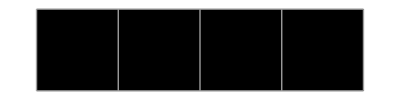
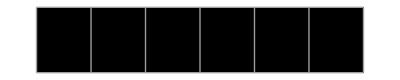
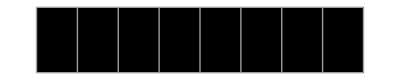
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[ArrayPlot[CellularAutomaton[{#,3},{Append[Table[1,n],2],0},{{200}}], Mesh->True],{n,3}]&/@ all[[;;3]]
```

```mathematica
ColorData[110][1]
```

RGBColor[0.3, 0.68, 0.88]

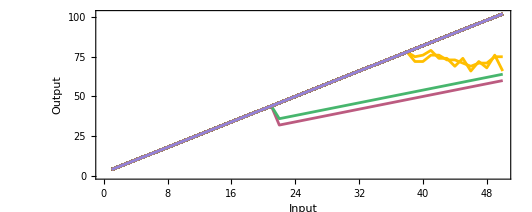

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[{#, 3},{Append[Table[1, i], 2], 0},{{{1000}}}], {i, 50}]&/@ all], PlotHighlighting->None, Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[{#, 3},{Append[Table[1, i], 2], 0},{{{1000}}}], {i, 50}]&/@ all], PlotHighlighting->None, Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
Table[Count[#, 1]&[CellularAutomaton[{#, 3},{Append[Table[1, i], 2], 0},{{{1000}}}]], {i, 50}]&/@ all[[;;1]]
```

{{4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,54,56,58,60,62,64,66,68,70,72,74,76,78,80,82,84,86,88,90,92,94,96,98,100,102}}

```mathematica
Length[all]
```

199

```mathematica
TakeLargestBy[ResourceData["Three-Color Cellular Automaton Rules that Double Their Input"],Length[First[FindTransientRepeat[CellularAutomaton[{#,3},{Append[Table[1,20],2],0},400],40]]]&,5]
```

{144892613592,5793483343212,6863658437061,6863916715200,7066073564883}

```mathematica
ArrayPlot[CellularAutomaton[{#,3},{Append[Table[1,20],2],0},1000]]&/@[[3;;4]]
```

{-Graphics-,-Graphics-}

```mathematica
(GraphicsRow[ArrayPlot[ArrayPad[#, 1]&/@ #]&/@Table[CellularAutomaton[{#, 3},{Append[Table[1, i], 2], 0},200], {i, 10}]])&/@ RandomSample[all, 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
data = ParallelTable[Count[#, 1]&[CellularAutomaton[{#, 3},{Append[Table[1, i], 2], 0},{{{1000}}}]], {i, 50}]&/@ all ;
```

```mathematica
data[[1, -1]]
```

102

```mathematica
Append[{-1}, #]&/@ Select[data, Last[#]=!= 102&->"Index"]
```

{{-1,37},{-1,157},{-1,178},{-1,179}}

```mathematica
ArrayPlot[CellularAutomaton[{all[[#]], 3}, {Append[Table[1, 50], 2], 0}, 2000]]&/@ Select[data, Last[#]=!= 102&->"Index"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
data[[All, -1]]
```

{102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,66,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,75,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,60,64,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102,102}

```mathematica
wc = MapAt[Callout[#, ArrayPlot[CellularAutomaton[{all[[#]], 3}, {Append[Table[1, 50], 2], 0}, 500]]]&,data,  Prepend[{-1}, #]&/@ Select[data, Last[#]=!= 102&->"Index"]];
```

```mathematica
ListLinePlot[wc]
```

-Graphics-

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[{#, 3},{Append[Table[1, i], 2], 0},{{{1000}}}], {i, 50}]&/@ all], PlotHighlighting->None, Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

### A Theory of Bugs

### Enumerating Fitness Landscapes